## Variable definitions

```mathematica
(*This is an initialization cell*)
Clear["Global`*"] (*Clear Previous History*)
Needs["PlotLegends`"]
Needs["NumericalCalculus`"]

a = 5.43*10^-10; (*lattice spacing*)
Com=10*10^11*10^-5/10^-4; (*elastic constant's order of magnitude*)
ℏ=1.055*10^-34;
kb=1.38*10^-23;
M = 28.0855*1.66054*10^-27; (*Mass of one silicon atom*)
β=1/kb/T;
```

## Calculation of RMS Motion

### Derivation

The average energy per atom can be written in the form
Average Energy per Atom=(2/πβ)∫_0^ξ y/(√(ξ^2-y^2))(1/(e^y-1)+1/2)ⅆy 
where the +1/2 is the ground state energy part. The deviation per atom is given by the square root of the average energy divided by the spring constant K.

First, calculate the ground state energy

```mathematica
ξ=2*β*ℏ*Sqrt[Kconstant/M];
groundEng=Assuming[{T>0, Kconstant>0},Integrate[y/Sqrt[ξ^2-y^2]*1/2,{y,0,ξ}]];
groundEng = groundEng*(2/π/β);
```

```mathematica
rmsMotion[temperature_,C11_, IncludeGroundState_]:=Module[{Kec, ξ,constantFactor,integrand, avgEnergy},
Kec=a*C11; (*Spring constant, we assume a potential of 1/2 kx^2*)
integrand = y/Sqrt[ξ^2-y^2]*(1/(Exp[y]-1));

ξ=2*β*ℏ*Sqrt[Kec/M];
constantFactor = 2/Pi/β;

avgEnergy=(constantFactor/.{T-> temperature})*NIntegrate[integrand/.{T-> temperature},{y,0,(ξ/.{T-> temperature})},
MaxRecursion-> 13]; (*The maxrecursion is needed because as y approaches ξ, the integrand becomes very small*)

If[IncludeGroundState == True, 
avgEnergy = avgEnergy+groundEng/.{ Kconstant-> Kec}];

(*Displacement in nm*)
Sqrt[avgEnergy/Kec]*10^12
];
```

### Results

Use this widget to get the RMS motion (in pm) for different temperatures

```mathematica
Manipulate[Re[rmsMotion[temperature, Com, True]],{temperature,10^-5,1},
FrameLabel-> { "Deviation in pm", "","Deviation vs temperature (in K)"}]
```

Plot of the results

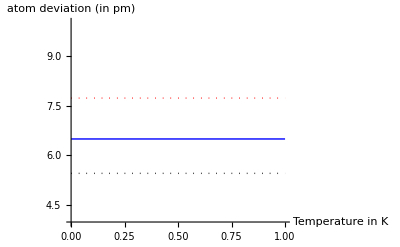

```mathematica
Plot[{Re[rmsMotion[tTemp,Com,True]], Re[rmsMotion[tTemp,Com/2, True]], Re[rmsMotion[tTemp,Com*2, True]]}, {tTemp, 10^-4, 1},
AxesLabel -> {"Temperature in K","atom deviation (in pm)"},
PlotStyle-> {Blue,{Red, Thick,Dotted}, {Black,Thick,Dotted}},
PlotLegend-> {"Avg elastic constant of 10^12dyn/cm^2","Lower Bound elastic constant of 0.5×10^12dyn/cm^2" , "Upper Bound elastic constant of 2×10^12dyn/cm^2"},
LegendPosition->{1,-0.4},
LegendShadow-> {0.01,-0.01},
LegendSize->{1.4,0.5},
(*PlotLabel-> "Ground state energy included",*)
PlotRange-> {Full,{4,10}}
]
```

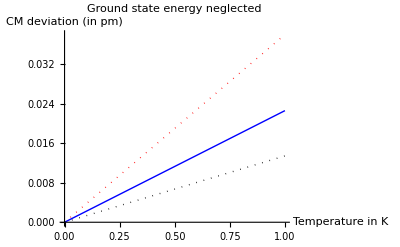

```mathematica
Plot[{Re[rmsMotion[tTemp,Com,False]], Re[rmsMotion[tTemp,Com/2, False]], Re[rmsMotion[tTemp,Com*2, False]]}, {tTemp, 10^-4, 10^0},
AxesLabel -> {"Temperature in K","CM deviation (in pm)"},
PlotStyle-> {Blue,{Red, Thick,Dotted}, {Black,Thick,Dotted}},
PlotLegend-> {"Avg Data","Upper Bound", "Lower Bound"},
LegendPosition->{1,-0.4},
LegendShadow-> {0.01,-0.01},
LegendSize->{1,0.5},
PlotLabel-> "Ground state energy neglected"
]
```

### Validation of Results

High temperature limit

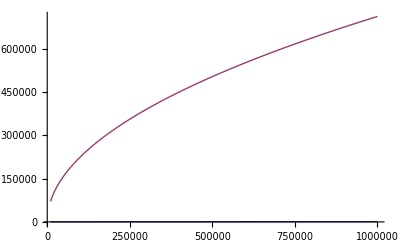

```mathematica
kecTemp = a*Com;
Plot[{Re[rmsMotion[tTemp, Com, False]],10^15*Sqrt[2*kb*tTemp/kecTemp]}, {tTemp, 10^4, 10^6}]
```

Low temperature limit

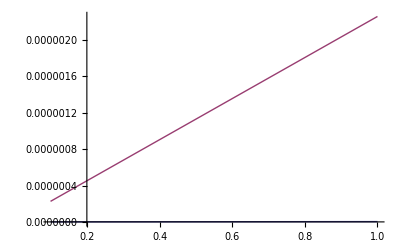

```mathematica
kecTemp = a*Com;
exprTempLow=Pi/12*(kb*tTemp)^2/ℏ/(Sqrt[kecTemp/M]*a)*a;
Plot[{Re[rmsMotion[tTemp, Com, False]],10^15*Sqrt[2*exprTempLow/kecTemp]}, {tTemp, 10^-8, 10^-7}]
```

Calculate the Debye temperature

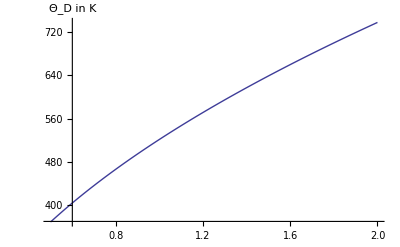

```mathematica
Plot[ℏ*2*Sqrt[a*Com*x/M]/kb,{x, 1/2,2},
AxesLabel-> {"","Θ_D in K"}]
```

Try to validate the heat capacity

```mathematica
avgEnergyAtom[temperature_,C11_, IncludeGroundState_]:=Module[{Kec, ξ,constantFactor,integrand, avgEnergy},
Kec=a*C11; (*Spring constant, we assume a potential of 1/2 kx^2*)
integrand = y/Sqrt[ξ^2-y^2]*(1/(Exp[y]-1));

ξ=2*β*ℏ*Sqrt[Kec/M];
constantFactor = 2/Pi/β;

avgEnergy=(constantFactor/.{T-> temperature})*NIntegrate[integrand/.{T-> temperature},{y,0,(ξ/.{T-> temperature})},
MaxRecursion-> 13]; (*The maxrecursion is needed because as y approaches ξ, the integrand becomes very small*)

If[IncludeGroundState == True, 
avgEnergy = avgEnergy+groundEng/.{ Kconstant-> Kec}];

avgEnergy
];
```

```mathematica
aTemp = 99*10^-0;
bTemp = 101*10^-0;
testHeatCapacity[T_,x_]:= 
Module[{aTemp,bTemp},

aTemp = T-T/150;
bTemp = T+T/150;(Re[avgEnergyAtom[aTemp, x*Com, False]]-Re[avgEnergyAtom[bTemp, x*Com, False]])/(aTemp-bTemp)
]
```

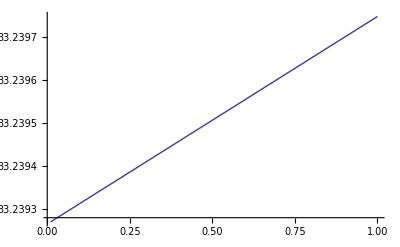

0.0000135028

```mathematica
Plot[10^3*6*10^23*testHeatCapacity[Sqrt[x],1]/Sqrt[x],{x,0.01,1}]
N[0.05*Sqrt[5]*10^-3/6/10^23/kb]
```

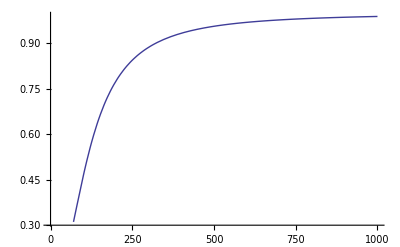

```mathematica
Plot[testHeatCapacity[x,1]/kb,{x,10^-3,1000}]
```

## Other less computationally efficient method ...

```mathematica
Econst = 2*ℏ/Pi*Sqrt[Kec/M];
expr = Abs[Sin[x]]*(1/(Exp[β*(ℏ*2*Sqrt[Kec/M]*Abs[Sin[x]])]-1));
% //TraditionalForm
```

Abs[sin(x)]/(ⅇ^((521.72 Abs[sin(x)])/T)-1)

```mathematica
Eavg=Econst*NIntegrate[expr/.{T-> 1},{x,-Pi/2,Pi/2}]
```

2.76996×10^-26